Radiation pressure + back-action evasion for nondegenerate internal squeezing

Attempt 1: Using Hamiltonian from Li et al, 2020

```mathematica
(*setting global assumptions*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0,β∈Reals,ρRP≥0,ρBAE≥0,αOG∈Reals,ϕ∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ);*)

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mc=(γc-ⅈ Ω)Id-(ⅈ ρBAE)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMc=Inverse[Mc]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 Inverse[Ma]-χ^2({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).Inverse[Mc].({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=Simplify[((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rb=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Ra=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rc=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(-χ)(2 γc)^(1/2)Γ.invMb.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.Inverse[Γ]),TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}})),TimeConstraint->TimeConstraint0];

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);
Sx=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs= Simplify[ComplexExpand[Abs[sigTransfer]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];
```

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

```mathematica
(*signal transfer function -- demonstration of factor of two*)
FullSimplify[(T.({{1}, {1}}))[[2]][[1]]/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG,ϕ->π/2}];
FullSimplify[(T.ConjugateTranspose[T])[[2,2]]/.{ρRP->0,ρBAE->0,Rpd->0,γa->0,γbtot->γR,γc->0,β->-αOG,ϕ->π/2}];
Print["sig. transfer fn.: ",Simplify[ComplexExpand[Abs[%%]^2]]," vs ", %]
```

sig. transfer fn.: (4 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2) vs (2 αOG^2 γR ωs^2)/(γR^2 Ω^2+(χ^2+Ω^2-ωs^2)^2)

```mathematica
(*R.P. turned off, but lossy:
does it reduce to lossy sWLC? yes!*)
Simplify[Sh/.{ρRP->0,ρBAE->0,β->-αOG,ϕ->π/2}/.ConjugateFlipI,TimeConstraint->{1,5}];
(*comparing to (ASDShsWLC)^2 from sWLC.nb*)
PSDShsWLC=1/((γc^2+Ω^2)4 αOG^2 ωs^2 γR)(
((γbtot-2γR)(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-(γbtot-2γR)(γa+γc)-γa γc+Ω^2)^2
+4γR γa ωs^2(γc^2+Ω^2)
+4γR γb(γa^2+Ω^2)(γc^2+Ω^2)
+4γR γc χ^2(γa^2+Ω^2)
+Rpd/(1-Rpd)((γbtot(γa γc-Ω^2)-(γa+γc)Ω^2+ωs^2 γc-χ^2 γa)^2
+Ω^2(χ^2-ωs^2-γbtot(γa+γc)-γa γc+Ω^2)^2));
(PSDShsWLC/.{γb->γbtot-γR})//FullSimplify
Print["Rad. pressure off, Sh reduces to lossy sWLC: ",ComplexExpand[%%%==%]//Simplify]
```

-1/(4 (-1+Rpd) αOG^2 γR (γc^2+Ω^2) ωs^2)((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)

Rad. pressure off, Sh reduces to lossy sWLC: True

```mathematica
(*want to show that Sx reduces to lossy sWLC (in order to inspect the denom),
simplfying assuming ϕ=π/2, have to start further back because simplifying Sx takes too long
--> i.e. applying Sx[[2,2]]/.ConjugateRepl just hangs, so use ConjugateFlipI*)
(*all variables are real, so tell .nb to expand conjugates just based on ⅈ*)
Sx022=Together[Sx[[2,2]]/.ϕ->π/2];
Sx022num=Collect[Numerator[Sx022]//Expand,{ρRP,ρBAE},FullSimplify]
Sx022denom=Denominator[Sx022]//Expand//FullSimplify
(*check that manipulation hasn't changed anything*)
Sx022==Sx022num/Sx022denom//Simplify
(*showing that poles are preserved, denom is similar enough
--> therefore stability is the same and pole-defined threshold values are the same*)
prevDenom=((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4);
(Sx022denom==Ω^4 prevDenom^2)//Simplify
(*for completeness, should show this for ϕ free but this will be tedious and should follow anyway*)
```

-8 (-1+Rpd) γR ρRP^2 (γc^2+Ω^2) ωs^2 (γa ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+(γc χ^2+γbtot (γc^2+Ω^2)) ωs^2)-8 (-1+Rpd) γR ρBAE^2 χ^2 (γa^2+Ω^2) ((γa^2+Ω^2) (γbtot (γbtot γc+χ^2)+γc Ω^2)+(γa (2 γbtot γc+χ^2)-2 γc Ω^2) ωs^2+γc ωs^4)+Ω^4 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4) ((γa^2+Ω^2) (-2 γbtot γc χ^2-8 (-1+Rpd) γc γR χ^2+γc^2 Ω^2+γbtot^2 (γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)+16 (-1+Rpd) γR ρBAE ρRP χ^2 ωs^2 (γa Ω^2 (4 γbtot γc-3 γc^2+χ^2+Ω^2)+γa^2 γc (γbtot γc+χ^2+3 Ω^2)+γa γc^2 ωs^2+Ω^2 (γbtot (-2 γc^2+Ω^2)+γc (-Ω^2+ωs^2)))

Ω^4 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2

True

True

```mathematica
(*signal transfer function is indep of RP and BAE and its denominator is exactly that from before,
NB: this is for the h (not h⃗) defintion, exactly what the h⃗ definition would be is unclear
--> the key difference between noise and signal is that for the noise the inputs are uncorrelated quadratures but for the signal the input is correlated h⃗, we could do everything wrt Subscript[X, 1,h] instead (where Subscript[X, 2,h]=0) which would yield the same result up to factors of 2*)
Block[{ϕ=π/2},
T0=Together[sigTransferAbs^2//Simplify]]
Denominator[T0]//FullSimplify
%==prevDenom
```

-((4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2)/(γa^2 γbtot^2 γc^2-2 γa^2 γbtot γc χ^2+γa^2 χ^4+γa^2 γbtot^2 Ω^2+γa^2 γc^2 Ω^2+γbtot^2 γc^2 Ω^2+2 γa^2 χ^2 Ω^2-2 γbtot γc χ^2 Ω^2+χ^4 Ω^2+γa^2 Ω^4+γbtot^2 Ω^4+γc^2 Ω^4+2 χ^2 Ω^4+Ω^6+2 γa γbtot γc^2 ωs^2-2 γa γc χ^2 ωs^2+2 γa γbtot Ω^2 ωs^2-2 γc^2 Ω^2 ωs^2-2 χ^2 Ω^2 ωs^2-2 Ω^4 ωs^2+γc^2 ωs^4+Ω^2 ωs^4))

(γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4

True

```mathematica
(*investigating BAE for ϕ≠±π/2, first: signal transfer function*)
Block[{sigT=Together[sigTransferAbs]},
numerT=Numerator[sigT];
denomT=Denominator[sigT];
(*sanity check
Print[numerT/denomT==Together[sigTransferAbs]];-->True*)]
(*notice that signal transfer function only changes if ϕ≠±π/2 and Subscript[ρ, BAE]≠0*)
numerTsqr=Collect[numerT^2,{ϕ,ρRP,ρBAE},FullSimplify]
denomTsqr=Collect[denomT^2,{ϕ,ρRP,ρBAE},FullSimplify]
(*sanity check
Simplify[numerTsqr==Numerator[Together[sigTransferAbs^2]]]
Simplify[denomTsqr==Denominator[Together[sigTransferAbs^2]]]
--> True True*)
```

16 β^2 (γR-Rpd γR) Ω^8 (γc^2+Ω^2) ωs^2 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)-16 √2 β^2 (γR-Rpd γR) ρBAE χ^2 Ω^6 ωs^2 ((γa^2+Ω^2) (γbtot (-γc^2+Ω^2)+γc (χ^2+2 Ω^2))+(-γa γc^2+(γa-2 γc) Ω^2) ωs^2) Sin[2 ϕ]-8 (-1+Rpd) β^2 γR ρBAE^2 χ^4 Ω^4 (γa^2+Ω^2) ωs^2 Sin[2 ϕ]^2

4 Ω^8 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2+16 ρBAE ρRP χ^2 Ω^4 ωs^2 (Ω (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))-γa (χ^2+γbtot (-γc+Ω)+Ω (γc+Ω))+(γc-Ω) ωs^2) (γbtot Ω (-γc+Ω)+γa (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))+Ω (χ^2+Ω (γc+Ω))-(γc+Ω) ωs^2) Cos[ϕ]^2+16 ρBAE^2 ρRP^2 χ^4 ωs^4 Cos[ϕ]^4

```mathematica
(*
Sx22===1+((...)+[complicated])/((…)+(…)ρRP ρBAE Cos[ϕ]^2+(…)(ρRP ρBAE Cos[ϕ]^2)^2);
sigTransferAbs^2===((…)+(…)ρRP ρBAE Sin[2ϕ]^2+(…)(ρRP ρBAE Sin[2ϕ]^2)^2)/((…)+(…)ρRP ρBAE Cos[ϕ]^2+(…)(ρRP ρBAE Cos[ϕ]^2)^2);
*)
```

```mathematica
(*
(*Want to look analytically at peaks of |T|^2*)
With[{dTdΩ=Together[D[numerTsqr/denomTsqr,Ω]]},
Collect[Numerator[dTdΩ],{ϕ,ρRP,ρBAE},Simplify]/Denominator[dTdΩ]]
*)
```

```mathematica
(*investigating BAE for ϕ≠±π/2, second: noise transfer function:
let ΔSx=Sx22-1 s.t. Sx11 = 1 + ΔSx
--> first problem is dealing with Conjugates in Sx22, which is now far faster due to ConjugateFlipI working on Sx for less than 5% of a second*)
Block[{
noiseΔSx=Together[Sx[[2,2]]-1],
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&},
numerΔSx=Collect[Numerator[noiseΔSx],{ϕ,ρRP,ρBAE},SimplifyConstrained];
denomΔSx=Collect[Denominator[noiseΔSx],{ϕ,ρRP,ρBAE},SimplifyConstrained];]
(*want to show that Sx is demonstrably real*)
(*common factor Exp[4ⅈ ϕ] accrued in numerator and denominator, cancel explictly --> formula is demonstrably real*)
commonFactor0=Exp[-4ⅈ ϕ];
numerΔSxSimpl=Collect[(commonFactor0 numerΔSx)//ExpToTrig,{ϕ,ρRP,ρBAE},FullSimplify]/.(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(4 ⅈ ϕ)))->2ⅈ Sin[2ϕ]
denomΔSxSimpl=Collect[(commonFactor0 denomΔSx)//ExpToTrig,{ϕ,ρRP,ρBAE},FullSimplify]
Print["same denom. as signal transfer fn?: ",denomTsqr==denomΔSxSimpl]
```

32 (-1+Rpd) γc γR χ^2 Ω^8 (γa^2+Ω^2) (-(γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2-(γc^2+Ω^2) ωs^4)-32 (-1+Rpd) γR ρBAE^2 χ^2 Ω^4 (γa^2+Ω^2) ((γa^2+Ω^2) (γbtot (γbtot γc+χ^2)+γc Ω^2)+(γa (2 γbtot γc+χ^2)-2 γc Ω^2) ωs^2+γc ωs^4) Sin[ϕ]^2+8 √2 (-1+Rpd) γR ρBAE χ^2 Ω^6 (γa^2+Ω^2) ((γa^2+Ω^2) (2 γbtot γc χ^2-3 γc^2 Ω^2+γbtot^2 (-3 γc^2+Ω^2)+(χ^2+Ω^2)^2)-2 (γa γc (3 γbtot γc-χ^2)+(-γa γbtot-3 γc^2+χ^2) Ω^2+Ω^4) ωs^2+(-3 γc^2+Ω^2) ωs^4) Sin[2 ϕ]+ρRP^2 (-32 (-1+Rpd) γR Ω^4 (γc^2+Ω^2) ωs^2 (γa ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+(γc χ^2+γbtot (γc^2+Ω^2)) ωs^2)+32 (-1+Rpd) γR ρBAE^2 χ^2 ωs^2 Cos[ϕ]^2 (-γa χ^2-2 γc ωs^2+γa χ^2 Cos[2 ϕ])+32 √2 (-1+Rpd) γR ρBAE χ^2 Ω^2 ωs^2 (γa γbtot (-γc^2+Ω^2)+γa γc (χ^2+2 Ω^2)+γc^2 ωs^2) Sin[2 ϕ])+ρRP (-16 (-1+Rpd) γR ρBAE χ^2 Ω^4 ωs^2 (-16 γa γbtot γc Ω^2+γa^2 (γbtot (γc-Ω) (γc+Ω)-5 γc (χ^2+2 Ω^2))+γa (γc-Ω) (γc+Ω) ωs^2+Ω^2 (γbtot (γc-Ω) (γc+Ω)+3 γc (χ^2+2 Ω^2-2 ωs^2))+(γa^2 (γc (5 γbtot γc-χ^2)-(γbtot-2 γc) Ω^2)+Ω^2 (-7 γbtot γc^2+3 γc χ^2+3 γbtot Ω^2+2 γc Ω^2-2 γc ωs^2)+γa (4 Ω^2 (-3 γc^2+χ^2+Ω^2)+(5 γc^2-Ω^2) ωs^2)) Cos[2 ϕ])+8 √2 (-1+Rpd) γR ρBAE^2 χ^2 Ω^2 ωs^2 (-γa^2 (4 γbtot γc+3 χ^2)+(4 γbtot γc+χ^2) Ω^2+γa γc (8 Ω^2-4 ωs^2)+χ^2 (γa^2+Ω^2) Cos[2 ϕ]) Sin[2 ϕ])

4 Ω^8 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2+16 ρBAE ρRP χ^2 Ω^4 ωs^2 (Ω (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))-γa (χ^2+γbtot (-γc+Ω)+Ω (γc+Ω))+(γc-Ω) ωs^2) (γbtot Ω (-γc+Ω)+γa (χ^2-γc Ω+Ω^2-γbtot (γc+Ω))+Ω (χ^2+Ω (γc+Ω))-(γc+Ω) ωs^2) Cos[ϕ]^2+16 ρBAE^2 ρRP^2 χ^4 ωs^4 Cos[ϕ]^4

same denom. as signal transfer fn?: True

```mathematica
(*BAE adds in complications that are too much for this project, let's drop it
--> sanity check denominator which appears to requires ρBAE unlike dIS, re-do derivation with no BAE to make sure*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γR>0,γc≥0,1>Rpd≥0,χ≥0,ωs>0,β∈Reals,ρRP≥0,αOG∈Reals,ϕ∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=αGW^2/(2^(1/2)ℏ μ);*)

Id=IdentityMatrix[2];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}});
invMa=Inverse[Ma]//Simplify;
Mc=(γc-ⅈ Ω)Id; (*manually removed BAE: -(ⅈ ρBAE)/(2^(1/2)Ω^2)({{1, 1}, {-1, -1}})*)
invMc=Inverse[Mc]//Simplify;
Mb=(γbtot-ⅈ Ω)Id+ωs^2 invMa-χ^2({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ=1/2^(1/2)({{1, 1}, {-ⅈ, ⅈ}});
Rin=Simplify[((1-Rpd)^(1/2)Γ.(Id-2 γR invMb).Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rb=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(2 (γbtot-γR))^(1/2)Γ. invMb.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Ra=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (2 γa)^(1/2)Γ. invMb.invMa.Inverse[Γ]),TimeConstraint->TimeConstraint0];
Rc=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)(-χ)(2 γc)^(1/2)Γ.invMb.({{0, ⅈ Exp[ⅈ ϕ]}, {-ⅈ Exp[-ⅈ ϕ], 0}}).invMc.Inverse[Γ]),TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[(-(1-Rpd)^(1/2)(2 γR)^(1/2)ωs (-ⅈ β)Γ. invMb.invMa.({{1, 0}, {0, -1}})),TimeConstraint->TimeConstraint0];

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);
Sx=Simplify[(
Rpd Id
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb]
+Rc.ConjugateTranspose[Rc])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}}))[[2]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs= Simplify[ComplexExpand[Abs[sigTransfer]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
Block[{noiseΔSx=Together[Sx[[2,2]]-1]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSx=Collect[Numerator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];
denomΔSx=Collect[Denominator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];]
Print["Sx = 1 + ",numerΔSx,"\n/\n",denomΔSx//Expand//FullSimplify,"\n"]

Block[{sigTsqr=Together[sigTransferAbs^2]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerTsqr=Collect[Numerator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];
denomTsqr=Collect[Denominator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];]
Print["|T|^2 = ",numerTsqr,"\n/\n",denomTsqr]
```

FullSimplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Sx = 1 + -8 (-1+Rpd) γR ρRP^2 (γc^2+Ω^2) ωs^2 (γa ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)+(γc χ^2+γbtot (γc^2+Ω^2)) ωs^2)-8 (-1+Rpd) γc γR χ^2 Ω^4 (γa^2+Ω^2) ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)
/
Ω^4 ((γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4)^2

|T|^2 = -4 (-1+Rpd) β^2 γR (γc^2+Ω^2) ωs^2
/
(γa^2+Ω^2) ((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)-2 (γa γc χ^2-γa γbtot (γc^2+Ω^2)+Ω^2 (γc^2+χ^2+Ω^2)) ωs^2+(γc^2+Ω^2) ωs^4

```mathematica
Sx/.{ωs->0,χ->γbtot x}//FullSimplify//MatrixForm
(*cf. nOPO:
({{1-(8 (-1+Rpd) x^2 κa^2 κaf κc)/(κa^2 (-x^2 κa+κc)^2+((1+2 x^2) κa^2+κc^2) Ω^2+Ω^4), 0}, {0, 1-(8 (-1+Rpd) x^2 κa^2 κaf κc)/(κa^2 (-x^2 κa+κc)^2+((1+2 x^2) κa^2+κc^2) Ω^2+Ω^4)}})*)
```

(1-(8 (-1+Rpd) x^2 γbtot^2 γc γR)/(γbtot^2 (-x^2 γbtot+γc)^2+((1+2 x^2) γbtot^2+γc^2) Ω^2+Ω^4) | 0
0 | 1-(8 (-1+Rpd) x^2 γbtot^2 γc γR)/(γbtot^2 (-x^2 γbtot+γc)^2+((1+2 x^2) γbtot^2+γc^2) Ω^2+Ω^4))

```mathematica
(*4x4 solution --> verifying RP and pump phase dependence (or lack thereof) of transfer functions*)
$Assumptions={Ω≥0,γa≥0,γbtot≥γbR>0,γctot≥γcR≥0,1>Rpd≥0,χ≥0,ωs≥0,β∈Reals,ρRP≥0,αOG∈Reals,ϕ∈Reals};
(*where β=(αGW Larm)/(2^(1/2)ℏ), ρRP=αGW^2/(2^(1/2)ℏ μ);*)

Id4=IdentityMatrix[4];
(*simplifying upstream to better the end result*)
Ma=(γa-ⅈ Ω)Id4+(ⅈ ρRP)/(2^(1/2)Ω^2)({{1, 1, 0, 0}, {-1, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
invMa=Inverse[Ma]//Simplify;
(*diagonal matrices are not in the centre of the matrix algebra, only multiples of the identity are --> silly mistake!*)
Mb=({{γbtot, 0, 0, 0}, {0, γbtot, 0, 0}, {0, 0, γctot, 0}, {0, 0, 0, γctot}})-ⅈ Ω Id4+χ({{0, 0, 0, ⅈ Exp[ⅈ ϕ]}, {0, 0, -ⅈ Exp[-ⅈ ϕ], 0}, {0, ⅈ Exp[ⅈ ϕ], 0, 0}, {-ⅈ Exp[-ⅈ ϕ], 0, 0, 0}})+ωs^2({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
TimeConstraint0={0.1,1};
invMb=Simplify[Inverse[Mb],TimeConstraint->TimeConstraint0];

Γ4=1/2^(1/2)({{1, 1, 0, 0}, {-ⅈ, ⅈ, 0, 0}, {0, 0, 1, 1}, {0, 0, -ⅈ, ⅈ}});
Rin=Simplify[(1-Rpd)^(1/2)Γ4.(Id4-2 ({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}})).Inverse[Γ4],TimeConstraint->TimeConstraint0];
Ra=Simplify[-(1-Rpd)^(1/2) 2ωs γa^(1/2) Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).Inverse[Γ4],TimeConstraint->TimeConstraint0];
Rb=Simplify[-(1-Rpd)^(1/2)2Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{(γbtot-γbR)^(1/2), 0, 0, 0}, {0, (γbtot-γbR)^(1/2), 0, 0}, {0, 0, (γctot-γcR)^(1/2), 0}, {0, 0, 0, (γctot-γcR)^(1/2)}}).Inverse[Γ4],TimeConstraint->TimeConstraint0];(*ϕ free in Hamiltonian, recover when ϕ=π/2*)
T=Simplify[-(1-Rpd)^(1/2)2^(1/2)ωs (-ⅈ β)Γ4.({{γbR^(1/2), 0, 0, 0}, {0, γbR^(1/2), 0, 0}, {0, 0, γcR^(1/2), 0}, {0, 0, 0, γcR^(1/2)}}).invMb.({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).invMa.({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),TimeConstraint->TimeConstraint0]; (*last matrix is more like ({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}).({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})*)

(*theorem: conjugation commutes with any holomorphic function that is real-valued on the reals, which is all the functions we care about (check this!), use FlipI only if all variables are real*)
(*look at //FullForm, ⅈ is not present in all forms, sometimes is just Complex[0,1]*)
(*:> is RuleDelayed: "represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used. "*)
FlipI={ⅈ->-ⅈ,Complex[RePart_,ImPart_]->Complex[RePart,-ImPart]};
(*FlipI should catch all cases (check this with FullForm?, how? --> will not work through Hold, so don't use that)*)
ConjugateFlipI=Conjugate[f_]:>(f/.FlipI);
Sx=Simplify[(
Rpd Id4
+Rin.ConjugateTranspose[Rin]
+Ra.ConjugateTranspose[Ra]
+Rb.ConjugateTranspose[Rb])/.ConjugateFlipI,TimeConstraint->{1,5}];
(*signal transfer function is Subscript[X, PD,2] wrt h not (X⃗)_PD wrt h⃗ --> factor of two from Subscript[(T.({{1}, {1}})), 22] versus Subscript[T, 22]
NB: another subtlety in that Subscript[T, 21]=Subscript[T, 22], but I don't know if this can be known a priori*)
sigTransfer = Simplify[(T.({{1}, {1}, {0}, {0}}))[[2]][[1]],TimeConstraint->{1,5}];(*[[1]] to remove atomic brackets {...}*)
sigTransferAbs= Simplify[ComplexExpand[Abs[sigTransfer]],TimeConstraint->{1,5}];
Sh=Simplify[Sx[[2,2]]/sigTransferAbs^2,TimeConstraint->{1,5}];
```

Simplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 5. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
Sx/.{ωs->0,γcR->0}//FullSimplify//MatrixForm
(%[[2,2]]/.{γbR->γR,γctot->γc})==1-(8 (-1+Rpd) γc γR χ^2)/((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)
(*cf. previously: ({{1-(8 (-1+Rpd) γc γR χ^2)/((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4), 0}, {0, 1-(8 (-1+Rpd) γc γR χ^2)/((-γbtot γc+χ^2)^2+(γbtot^2+γc^2+2 χ^2) Ω^2+Ω^4)}})*)
(*correlations not seen because γcR turned off*)
```

(1-(8 (-1+Rpd) γbR γctot χ^2)/((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4) | 0 | 0 | 0
0 | 1-(8 (-1+Rpd) γbR γctot χ^2)/((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

True

```mathematica
Block[{noiseΔSx=Together[Sx[[2,2]]-1]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerΔSx4x4=Collect[Numerator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];
denomΔSx4x4=Collect[Denominator[noiseΔSx],{ϕ,ρRP},SimplifyConstrained];]
Print["Sx = 1 + ",numerΔSx4x4,"\n/\n",denomΔSx4x4//Expand//FullSimplify,"\n"]

Block[{sigTsqr=Together[sigTransferAbs^2]},
SimplifyConstrained=FullSimplify[#,TimeConstraint->{0.1,1}]&;
numerTsqr4x4=Collect[Numerator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];
denomTsqr4x4=Collect[Denominator[sigTsqr],{ϕ,ρRP},SimplifyConstrained];]
Print["|T|^2 = ",numerTsqr4x4,"\n/\n",denomTsqr4x4]
```

FullSimplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Sx = 1 + -8 (-1+Rpd) γbR ρRP^2 (γctot^2+Ω^2) ωs^2 (γa ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)+(γctot χ^2+γbtot (γctot^2+Ω^2)) ωs^2)-8 (-1+Rpd) γbR γctot χ^2 Ω^4 (γa^2+Ω^2) ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)
/
Ω^4 ((γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4)^2

|T|^2 = -4 (-1+Rpd) β^2 γbR (γctot^2+Ω^2) ωs^2
/
(γa^2+Ω^2) ((-γbtot γctot+χ^2)^2+(γbtot^2+γctot^2+2 χ^2) Ω^2+Ω^4)-2 (γa γctot χ^2-γa γbtot (γctot^2+Ω^2)+Ω^2 (γctot^2+χ^2+Ω^2)) ωs^2+(γctot^2+Ω^2) ωs^4

```mathematica
(*do these reduce to previous calculations, i.e. have I verified that ρRP does not appear in the denominator for nIS?*)
numerΔSx/denomΔSx==(numerΔSx4x4/denomΔSx4x4/.{γbR->γR,γcR->0,γctot->γc})//Simplify
numerTsqr/denomTsqr==(numerTsqr4x4/denomTsqr4x4/.{γbR->γR,γcR->0,γctot->γc})//Simplify
```

True

True

```mathematica
(*-------------------------------------------------------------------------------------------------------------------*)
(*plot params -- from sWLC model*)
c=3. 10^8(*ms^-1*);
ℏ=1. 10^-34(*Js*);
Larm=4. 10^3(*m*);
Pcirc=3. 10^6(*J/s*);
λ0=2. 10^-6(*m*);
ω0=2π c/λ0;
γR=2π 500.(*Hz*);
ωs=10γR;
τRoundTripArm=(2 Larm)/c;
Tsrm=0.046; (*assuming LIGO Voyager's Subscript[T, SRM] was used for γR*)
τRoundTripSRC=-1/(2 γR)Log[1-Tsrm];
β=-((2Pcirc Larm ω0)/(ℏ c))^(1/2);(*rescaling of α by 1/(2^(1/2)ℏ) seems to be in Li?, chosen β s.t. turning R.P. off should match
β=(αGW Larm)/(2^(1/2)ℏ);
ρRP=ρBAE=αGW^2/(2^(1/2)ℏ μ)=(2^(1/2)ℏ β^2)/(Larm^2 μ); but |α|=|αGW Larm|*)
M=200.(*kg*);
μ=M/4;
ρ=(2^(1/2)ℏ β^2)/(Larm^2 μ);
γaFn[Tla_]:=-1/(2 τRoundTripArm)Log[1-Tla]
γbtotFn[Tlb_]:=γR+-1/(2 τRoundTripSRC)Log[1-Tlb]
γcFn[Tlc_,symSRM_]:=If[symSRM,γR+-1/(2 τRoundTripSRC)Log[1-Tlc],-1/(2 τRoundTripSRC)Log[1-Tlc]]
(*plotting sensitivity -- un-simplified Sh*)
(*taking real part to discard numerical error creating tiny imaginary parts*)
QNwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[Sx[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
sigwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[sigTransferAbs]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
ASDShwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[Sh]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
```

```mathematica
legendStyler[vals0_]:=(
If[Length[vals0]==6,vals=Join[vals0,{True,True,False}],vals=vals0];
paddedStrings=
Insert[StringPadRight[{ToString[N[vals[[1]]/ωs]],ToString[vals[[3]]],ToString[vals[[4]]],ToString[vals[[5]]],ToString[vals[[6]]]},4],StringPadRight[ToString[N[vals[[2]]/(2π)]],5],2];
(*<> is StringJoin*)
Style[StringForm["χ/ωs=``, "<>ToString[If[Mod[vals[[2]]-π/2,π]==0,StringPadRight[ToString[StringForm["ϕ=``π/2",If[Mod[vals[[2]]-π/2,2π]==0,"+","-"]]],12],StringForm["ϕ/(2π)=``",
paddedStrings[[2]]]]]<>"; T_(l, a)=``, T_(l, b)=``"
<>If[vals[[9]],", γ_(c, tot)=γ_R+γ_c(T_(l, c)=``)",", T_(l, c)=``"]
<>", R_PD=``"
<>If[Not[vals[[7]]],"; no RP",""]
<>If[Not[vals[[8]]],"; no BAE",""],
paddedStrings[[1]],
paddedStrings[[3]],
paddedStrings[[4]],
paddedStrings[[5]],
paddedStrings[[6]]],
FontFamily->"Monospace"])

plotwRP[valsList_,plotLabel_:None,plotStyle_:{},fRange_:{10^0,10^5}]:=(
{fmin,fmax}=fRange;
p1=LogLinearPlot[Evaluate[Table[20Log10[QNwRP@@Join[{2π f},valsList[[i]]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,
ImagePadding->{{100,10},{1,All}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{,If[ToString[plotLabel]==ToString[None],"nondegenerate internal squeezing\nparameters of LIGO Voyager",plotLabel]}},
PerformanceGoal->"Speed"];
p2=LogLogPlot[Evaluate[Table[sigwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{1,1}},TicksStyle->{Directive[FontOpacity->0,FontSize->0],},PlotRange->{{fmin,fmax},All},PlotStyle->plotStyle,Frame->True,FrameLabel->{{"signal transfer function,\n|T| / [?] (log scale)",},{,}},
PerformanceGoal->"Speed"];
p3=LogLogPlot[Evaluate[Join[
Table[ASDShwRP@@Join[{2π f},valsList[[i]]],{i,1,Length[valsList]}],
{If[10^3<#<4 10^3,5 10^-25,Null]&[f]}]],
{f,fmin,fmax},ImageSize->350,ImagePadding->{{100,10},{All,1}},PlotLegends->LineLegend[Join[Table[legendStyler[valsList[[i]]],{i,1,Length[valsList]}],{"5×10^-25Hz^(-1/2) target for 1–4 kHz"}],LabelStyle->Directive[10],LegendMarkerSize->{{25,15}}],PlotStyle->({q0,r0}=If[plotStyle≠{},QuotientRemainder[Length[valsList],Length[plotStyle]],{0,Length[valsList]}];
Join[Flatten[Table[plotStyle,{i,1,q0}],1],Table[,{i,1,r0}],{Directive[Red,DotDashed]}]),PlotRange->{{fmin,fmax},All},Filling->{Length[valsList]+1->Bottom},Frame->True,FrameLabel->{{"strain sensitivity (NSR)\n/ Hz^(-1/2) (log scale)",},{"frequency, f=Ω/(2  π) / Hz (log scale)",}},
PerformanceGoal->"Speed"];
Column[{p1,p2,p3},Spacings->0])
(*plotting function appears slow,
to-do: speed up plotter by simplifying functions, particularly QNwRP?*)
```

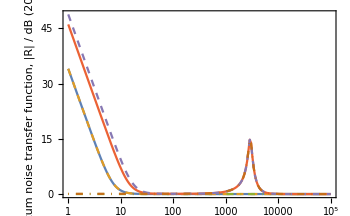
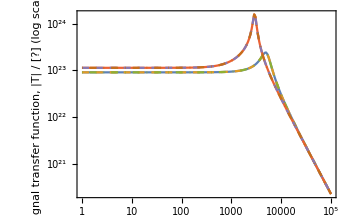
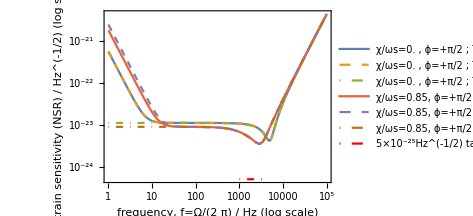

```mathematica
χRatio0=0.85;
pumpPhase0=1/2 π;
valsList1={
{0,pumpPhase0,0.1,0.1,0.1,0.1},
{0,pumpPhase0,0.1,0.1,0.1,0.1,True,False,False},
{0,pumpPhase0,0.1,0.1,0.1,0.1,False,False,False},
{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1},
{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,True,False,False},
{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,False,False,False}};
plotwRP[valsList1,None,{,Dashed,DotDashed}]
(*checked that the there is no double peak -- looks the same with PerformanceGoal->Quality
to-do: for completeness, should find all local maxima -- maybe part of threshold plots?
plotwRP[valsList1,None,{,Dashed,DotDashed},{2 10^3,4 10^3}]*)
(*DC response, graph got deleted in a crash --> suffice to say that linear Ω graph showed that for ϕ≠π/2, signal goes to zero and QN goes to a constant non-zero value*)
(*BAE doesn't look like Fig. 5 in Lietal2020 --> that graph has thermal noise but where is the large LF improvement?*)
```

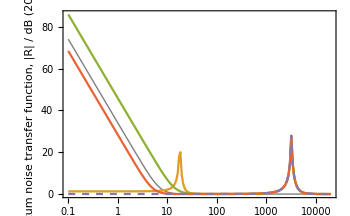
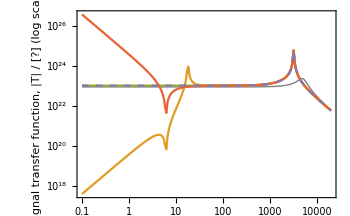
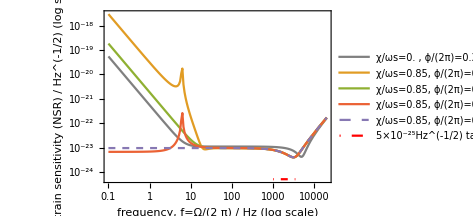

```mathematica
χRatio0=0.85;
pumpPhase0=(3π)/4;
valsList1={
{0,pumpPhase0,0.1,0.1,0.1,0.1,True,True,True},
{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,True,True,True},
{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,True,False,True},
{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,False,True,True},
{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,False,False,True}};
plotwRP[valsList1,None,{{Gray,Thickness[Medium]},,,,Dashed},{10^-1,2 10^4}]
```

```mathematica
(*however, there are multiple peaks, when we look off ϕ=+-π/2
--> this appears to requires BAE*)
(*to-do: sweeping through ϕ with Manipulate in order to see the effects of BAE*)
(*pumpPhase1=3/4 π;*)
(*
Manipulate[
valsList1={
{0,pumpPhase1,0.1,0.1,0.1,0.1,True,True,True},
{χRatio0 ωs,pumpPhase1,0.1,0.1,0.1,0.1,True,True,True},
{χRatio0 ωs,pumpPhase1,0.1,0.1,0.1,0.1,True,False,True},
{χRatio0 ωs,pumpPhase1,0.1,0.1,0.1,0.1,False,False,True}};
plotwRP[valsList1,None,{},{5 10^-1,10^5}],{{pumpPhase1,3/4 π},0,2π}]
*)
(*plotting for symmetric losses since then expect ϕ->+-π to be a symmetry*)
```

```mathematica
(*NB: radiation pressure worsened because squeezing is in phase quadrature,
to-do: frequency dependent internal squeezing?
--> we now have pump parameter -- so use /.ϕ->ϕFn[...]?*)
```

```mathematica
(*to-do: copy other plotting functions from sWLC:,
- stability --> not necessary, same denominator in transfer functions so same stability,
- noise "budget" (transfer functions) --> done, but I don't know how to turn off shot noise? ,
- optimum sensitivity at probe frequency --> done, 2.5k is most interesting,
*)
```

```mathematica
(*noise "budget",
to-do: turn shot noise off to plot radiation pressure separately, how?*)
RpdwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rpd Id)[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RinwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rin.ConjugateTranspose[Rin])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RawRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Ra.ConjugateTranspose[Ra])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RbwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rb.ConjugateTranspose[Rb])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}
RcwRP[Ω0_,χ0_,ϕ0_,Tla_,Tlb_,Tlc_,Rpd0_,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=Re[Sqrt[(Rc.ConjugateTranspose[Rc])[[2,2]]]]/.{
Ω->Ω0,χ->χ0,ϕ->ϕ0,γa->γaFn[Tla],γbtot->γbtotFn[Tlb],γc->γcFn[Tlc,symSRM],Rpd->Rpd0,ρRP->If[ρRPTrue,ρ,0],ρBAE->If[ρBAETrue,ρ,0]}

plotNoiseBudgetwRP[params_,fRange_:{1,10^5}]:=
LogLinearPlot[Evaluate[{
20Log10[1],
20Log10[RinwRP@@Join[{2π f},params]],
20Log10[RawRP@@Join[{2π f},params]],
20Log10[RbwRP@@Join[{2π f},params]],
20Log10[RcwRP@@Join[{2π f},params]],
20Log10[RpdwRP@@Join[{2π f},params]],
20Log10[QNwRP@@Join[{2π f},params]]}],{f,fRange[[1]],fRange[[2]]},PlotLegends->LineLegend[{"vacuum","R_in, behind SRM","(R^(L))_a, arm intra-cav.","(R^(L))_b, SRC signal intra-cav.","(R^(L))_c, SRC idler intra-cav.","(R^(L))_PD, PD loss","total quantum noise"},LabelStyle->Directive[10],LegendLabel->legendStyler[params]],PlotRange->All,PlotStyle->{Directive[Gray,Dashed],,,,,,Directive[Black,Dashed]},Frame->True,FrameLabel->{{"quantum noise transfer function,\n|R| / dB (20log10)",},{"frequency, f=Ω/(2  π) / Hz","nondegenerate internal squeezing\nparameters of LIGO Voyager"}},PerformanceGoal->"Speed"]
```

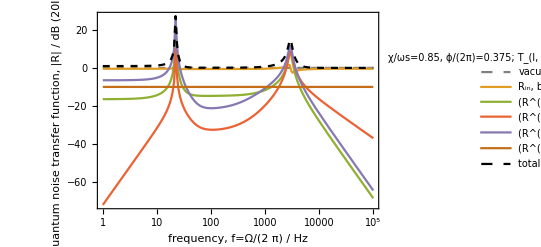

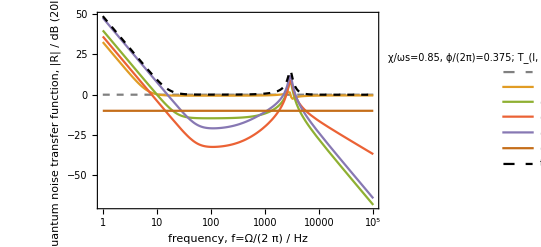

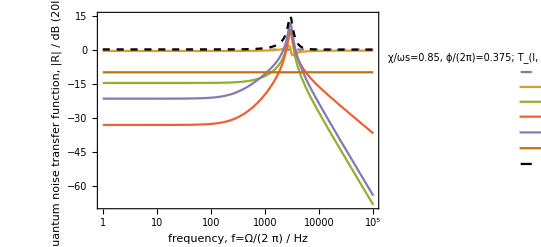

```mathematica
χRatio0=0.85;
pumpPhase0=3/4 π;
plotNoiseBudgetwRP[{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1}]
plotNoiseBudgetwRP[{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,True,False,False}]
plotNoiseBudgetwRP[{χRatio0 ωs,pumpPhase0,0.1,0.1,0.1,0.1,False,False,False}]
(*BAE 2nd peak (if real, not a bug) appears in all noise transfer functions (except Rpd ofc)*)
```

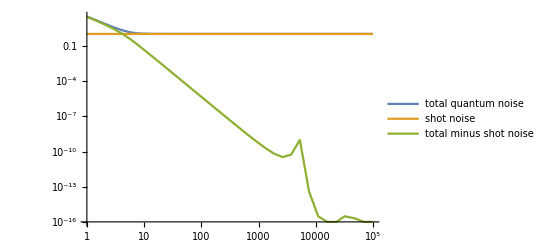

```mathematica
(*to-do: turn shot noise off (how?) to plot radiation pressure separately
--> only a low quality plot, don't draw any conclusions*)
LogLogPlot[Evaluate[{
QNwRP[2π f,0,π/2,0,0,0,0],
QNwRP[2π f,0,π/2,0,0,0,0,False,False,False],
QNwRP[2π f,0,π/2,0,0,0,0]-QNwRP[2π f,0,π/2,0,0,0,0,False,False,False]}],
{f,1,10^5},PerformanceGoal->"Speed",PlotRange->All,PlotPoints->5,PlotLegends->LineLegend[{"total quantum noise","shot noise","total minus shot noise"},LabelStyle->Directive[10]]]
```

```mathematica
(*optimum sensitivity at probe frequency
to-do: update this for pump phase freedom some time?*)
plotThresholdFinder[fProbe_,Tlc_,ϕ_:π/2,pastThreshold_:False,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False]:=(
probeNoiseRef=QNwRP[2π fProbe,0,ϕ,0,0,0,0,ρRPTrue,ρBAETrue,False];(*reference has no γc loss*)
probeSigRef=sigwRP[2π fProbe,0,ϕ,0,0,0,0,ρRPTrue,ρBAETrue,False];
probeSensRef=ASDShwRP[2π fProbe,0,ϕ,0,0,0,0,ρRPTrue,ρBAETrue,False];
rpdList=Subdivide[0,0.5,5];
p1=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["SNR (Hz^(1/2)) gain at `` kHz\nrelative to no loss/sqz. / dB (20 log_10(1/S_h))",N[fProbe/10^3]],},{,"nondegenerate internal squeezing\nparameters of LIGO Voyager"}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/ωs∈(0,1), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10],LegendLabel->StringForm["T_(l, c)=``, ϕ/(2π)=``"<>If[Not[ρRPTrue],"; no RP",""]<>If[Not[ρBAETrue],"; no BAE",""],NumberForm[N[Tlc]],NumberForm[N[ϕ/(2π)]]]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,AspectRatio->1,PerformanceGoal->"Speed"];
p2=ParametricPlot[Evaluate[{
{-20Log10[QNwRP[2π fProbe,1 ωs,ϕ,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,1 ωs,ϕ,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}}],{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{StringForm["χ/ωs=1, varying R_PD∈(``,``)",NumberForm[N[rpdList[[1]]]],NumberForm[N[rpdList[[-1]]]]]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
If[pastThreshold,
p1b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],-20Log10[ASDShwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSensRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotLegends->LineLegend[{Table[StringForm["χ/ωs∈(1,2), R_PD=``",NumberForm[N[rpdList[[i]]]]],{i,1,Length[rpdList]}]},LabelStyle->Directive[10]],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p1and2=Show[p1,p1b,p2];,
p1and2=Show[p1,p2];];
p3=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,0,1},Frame->True,FrameLabel->{{StringForm["signal transfer function |T| at `` kHz\nrelative to no loss/sqz. / dB (20 log_10)",N[fProbe/10^3]],},{StringForm["quantum noise transfer function |R| at `` kHz\nrelative to no loss/sqz. / dB (-20 log_10)",N[fProbe/10^3]],}},PlotStyle->Table[Blend[{Blue,Green},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{All,1}},ImageSize->350,AspectRatio->3/4,PerformanceGoal->"Speed"];
p4=ParametricPlot[Evaluate[
{-20Log10[QNwRP[2π fProbe,1ωs,ϕ,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],
20Log10[sigwRP[2π fProbe,1ωs,ϕ,0,0,Tlc,Rpd,ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}],{Rpd,rpdList[[1]],rpdList[[-1]]},Frame->True,PlotStyle->Directive[Black,Dashed],PlotRange->All,ImagePadding->{{80,10},{All,1}}];
If[pastThreshold,
p3b=ParametricPlot[Evaluate[Flatten[Table[{
{-20Log10[QNwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeNoiseRef],20Log10[sigwRP[2π fProbe,χRatio ωs,ϕ,0,0,Tlc,rpdList[[i]],ρRPTrue,ρBAETrue,symSRM]/probeSigRef]}},{i,1,Length[rpdList]}],1]],{χRatio,1,2},Frame->True,PlotStyle->Table[Blend[{Red,Yellow},(i-1)/Length[rpdList]],{i,1,Length[rpdList]}],PlotRange->All,ImagePadding->{{80,10},{1,All}},ImageSize->350,PerformanceGoal->"Speed"];
p3and4=Show[p3,p3b,p4];,
p3and4=Show[p3,p4];];
Column[{p1and2,p3and4},Spacings->0])
```

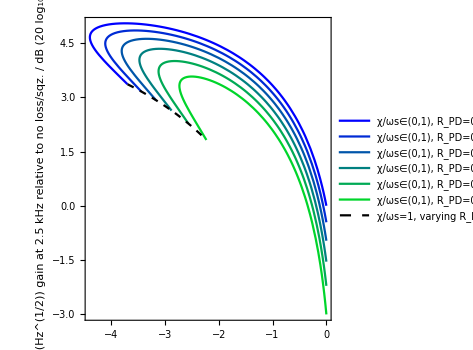
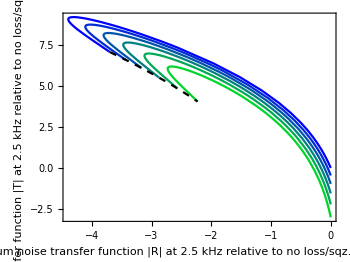

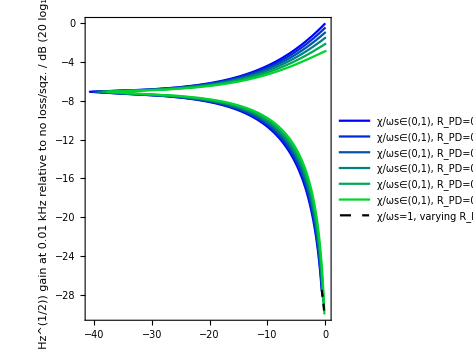
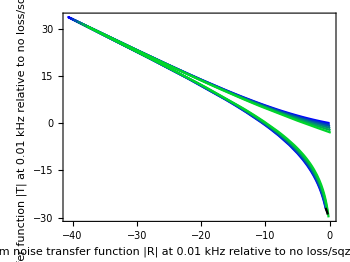

```mathematica
(*fProbe_,Tlc_,ϕ_:π/2,pastThreshold_:False,ρRPTrue_:True,ρBAETrue_:True,symSRM_:False*)
pumpPhase0=3/4 π;
plotThresholdFinder[2500(*Hz*),0.1,pumpPhase0]
plotThresholdFinder[10(*Hz*),0.1,pumpPhase0]
(*pump phase really affects low probe frequencies, but leaves kilohertz sensitivity relatively unchanged*)
```

```mathematica
(*to-do: stability plot for signal transfer function, but χ vs Ω, want to investigate LF peaks when BAE turned on
--> look at nIS.nb for starter*)
```